```mathematica
(**) Use methods defined in lecture 3 for Foward Euler Method and Midpoint Method
EulerForward[n_,f_,u0_,T_]:=Module[{u,Δt},
Δt = N[T/n];
u[0] = u0; 
u[i_]:= u[i] = u[i-1] + Δt f[u[i-1],(i-1) Δt];
Table[{i Δt, u[i]},{i,0,n}]
]
EulerForward::usage ="EulerForward[n,f,u0,T] integrates in 'n' steps the 1st order ODE u_t= f(u(t),t) in the interval 0<t<T using Euler Forward Method";
```

3 and defined Euler for Foward in lecture Method^2 methods Midpoint Use

```mathematica
MidPointRule[n_,f_,u0_,u1_,T_]:=Module[{u,Δt},
Δt = N[T/n];
u[0] = u0; 
u[1] = u1;
u[i_]:= u[i] = u[i-2] + 2Δt f[u[i-1],(i-1) Δt];
Table[{i Δt, u[i]},{i,0,n}]
]
MidPointRule::usage ="MidPointRule[n,f,u0,u1,T] integrates in 'n' steps the 1st order ODE u_t= f(u(t),t) in the interval 0<t<T using the MidPoint Rule, it requires u[0] and u[1]";

(**) Analytical Solution
```

Analytical Solution

{u[t]→1. ⅇ^(-0.5 t)}

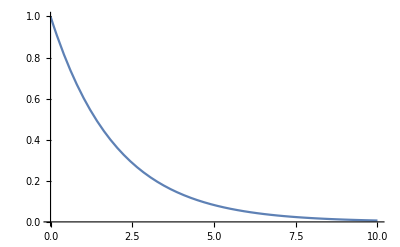

```mathematica
f[u_, t_] := -0.5u[t]
T= 10;
u0 = 1;
uExact = DSolve[{u'[t] == f[u,t],u[0] == 1}, u[t], t]//Flatten
pExact = Plot[u[t]/. uExact, {t,0,T}]
```

Numerical Solution

1/10

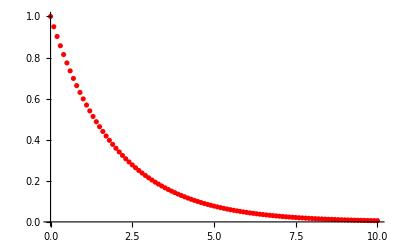

```mathematica
(**) Numerical Solution
f[u_,t_] := -0.5u
n=100;
Δt = T/n
uNum = EulerForward[n,f,u0, T];
pNum = ListPlot[uNum,PlotStyle-> {Red}]
```

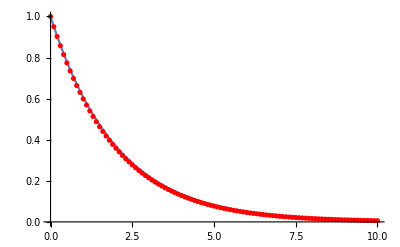

```mathematica
Show[pExact,pNum]
```